```mathematica
NFW[x_]:=1/x(Log[x/2]+Piecewise[{{2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))], 0≤x≤ 1}, {1, x==1}, {2/(√(x^2-1))ArcTan[√((x-1)/(1+x))], x>1}}])
```

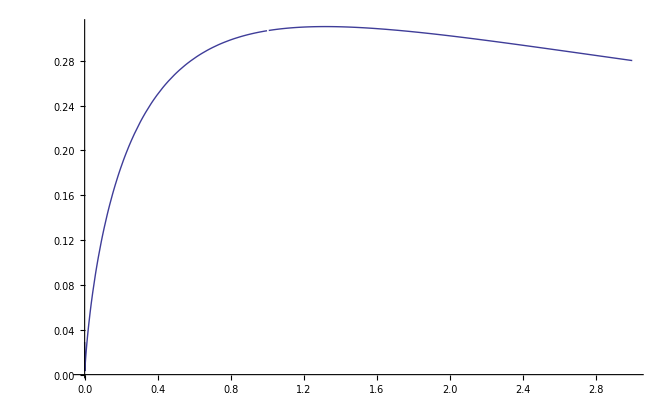

```mathematica
Plot[NFW[x],{x,0,3},PlotRange->All]
```